## Chapter 6

## Section 6.1

### Wallis Product

π/2==(2 2)/(1 3)*(4 4)/(3 5)*(6 6)/(5 7)*

```mathematica
Sin[Pi/2]/Pi/2
```

1/(2 π)

```mathematica
1/{(1-1/2),1+1/2,1-1/4,1+1/4}
```

{2,2/3,4/3,4/5}

### Exercise 6.1.1

Using

(sin(π x))/(π x)==(1-x^2/1) (1-x^2/4) (1-x^2/9)

and

(sin(π x))/(π x)==1-(π^2 x^2)/6+(π^4 x^4)/120+

The term proportional to x^4 in the product is going to be the sum

1/1^2*(1/2^2+1/3^2+)+1/2^2(1/3^2+1/4^2+)+

where the sums are set up so that only terms of the form

1/(m^2 n^2)

with m ≠ n appear. This can be written as a double sum over all m and n as long as we remember to divide by 2 (overcounting) and subtract out the terms of the form

1/n^4

1/2 (∑_m^∞ ∑_n^∞ 1/(m^2 n^2)-∑_n^∞ 1/n^4)==1/2 ((∑_m^∞ 1/m^2)(∑_n^∞ 1/n^2)-∑_n^∞ 1/n^4)==1/2((ζ(2))^2-ζ(4))

which gives

ζ(4)==π^4/36-2 π^4/120==π^4/90

```mathematica
Zeta[4]
```

π^4/90

## Section 6.2

```mathematica
SeriesCoefficient[x/(Exp[x]-1),{x,0,n}]
```

Piecewise[{{BernoulliB[n]/(n!), n≥0}, {0, True}}]

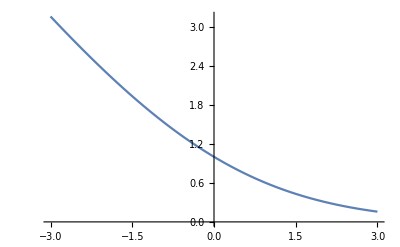

```mathematica
Plot[x/(Exp[x]-1),{x,-3,3}]
```

```mathematica
𝒮[m_Integer?NonNegative,n_]:=
Sum[k^m,{k,1,n-1}]
```

```mathematica
𝒮[1,n]
```

1/2 (-1+n) n

```mathematica
𝒮[2,n]
```

1/6 (-1+n) n (-1+2 n)

### Exercise 6.2.1

3 𝒮_2(n)==∑_(k=0)^m k Binomial[2+1, k] n^(3-k)==Binomial[3, 0] n^3-1/2 Binomial[3, 1] n^2+1/6 Binomial[3, 2] n+0 Binomial[3, 3]==n^3-3/2 n^2+1/2 n==(n(n-1)(2n-1))/2

### Exercise 6.2.2

x==(exp(x)-1) ∑_(k=0)^∞ (k x^k)/(k!)==(∑_(j=1)^∞ x^j/(j!))(∑_(k=0)^∞ (k x^k)/(k!))==(∑_(j=1)^∞ x^j/(j!))(∑_(k=0)^∞ (k x^k)/(k!))

Reindexing j→j+1 gives

x==(∑_(j=0)^∞ x^(j+1)/((j+1)!))(∑_(k=0)^∞ (k x^k)/(k!))==∑_(m=0)^∞ x^(m+1) ∑_(k=0)^m k/(k! (m+1-k)!)

This implies that

∑_(k=0)^m k/(k! (m+1-k)!)==m,0

Multiplying through by (m+1)! is harmless, since (0+1)!==1 and the right-hand side is zero for every other m, gives

∑_(k=0)^m k Binomial[m+1, k]==m,0

### Exercise 6.2.3

We have

0 Binomial[5, 0]+1 Binomial[5, 1]+2 Binomial[5, 2]+3 Binomial[5, 3]+4 Binomial[5, 4]==5 4+(5 (-1))/2+10/6+0 10+1 1==0

This implies

4==-1/5 ((5 (-1))/2+10/6+0 10+1 1)==-1/30

```mathematica
BernoulliB[4]
```

-1/30

```mathematica
Sum[Binomial[7,k]BernoulliB[k],{k,0,5}]+Binomial[7,6]ℬ[6]==0
```

-1/6+7 ℬ[6]==0

```mathematica
Solve[Sum[Binomial[7,k]BernoulliB[k],{k,0,5}]+Binomial[7,6]ℬ[6]==0,ℬ[6]]
```

{{ℬ[6]→1/42}}

```mathematica
BernoulliB[6]
```

1/42

### Exercise 6.2.4

𝒮_m(n)==1/(m+1)∑_(k=0)^m Binomial[m+1, k] k n^(m+1-k)

```mathematica
1/(m+1)Sum[Binomial[m+1,k]BernoulliB[k]n^(m+1-k),{k,0,m}]/.Map[{m->#}&,{4,5,6}]//Simplify
```

{1/30 n (-1+10 n^2-15 n^3+6 n^4),1/12 (-1+n)^2 n^2 (-1-2 n+2 n^2),1/42 (n-7 n^3+21 n^5-21 n^6+6 n^7)}

## Section 6.3

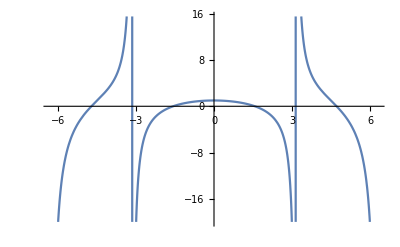

```mathematica
Plot[z Cot[z],{z,-2Pi,2Pi}]
```

```mathematica
SeriesCoefficient[z Cot[z],{z,0,n}]
```

Piecewise[{{1, n==0}, {(ⅈ^n 2^(-1+n) (1+(-1)^n) BernoulliB[n])/(n!), n≥1}, {0, True}}]

```mathematica
SeriesCoefficient[ Cot[z],{z,0,n}]
```

Piecewise[{{1, n==-1}, {-(ⅈ (2 ⅈ)^n (-1+(-1)^n) BernoulliB[1+n])/((1+n)!), n≥0}, {0, True}}]

```mathematica
1+Sum[BernoulliB[2n]x^(2n)/(2n)!,{n,1,Infinity}]
```

1+1/2 (-2+x Coth[x/2])

```mathematica
FullSimplify[%==x/2(Exp[x/2]+Exp[-x/2])/(Exp[x/2]-Exp[-x/2])]
```

True

```mathematica
Reduce[Cot[z+Pi]==Cot[z]]
```

True

```mathematica
Reduce[Cot[z+Pi/2]==-Tan[z]]
```

True

```mathematica
TrigExpand[{Cos[2z],Sin[2z]}]
```

{Cos[z]^2-Sin[z]^2,2 Cos[z] Sin[z]}

```mathematica
TrigExpand[2Cot[2z]]
```

Cot[z]-Tan[z]

```mathematica
c^2/(c s)
```

c/s

```mathematica
TrigReduce[Cot[z]==(Cot[z/2]+Cot[z/2+Pi/2])/2]
```

Cot[z]==1/2 Cos[z] Csc[z/2] Sec[z/2]

```mathematica
FullSimplify[%]
```

True

```mathematica
FullSimplify[Sum[Cot[(z+k*Pi)/2^n],{k,0,2^n-1}]/2^n,Assumptions->{n∈Integers,1≤n}]
```

-ⅈ (1+1/Log[ⅇ^(ⅈ 2^(1-n) π)]2^(1-n) (QPolyGamma[0,-Log[ⅇ^(-ⅈ 2^(1-n) z)]/Log[ⅇ^(ⅈ 2^(1-n) π)],ⅇ^(ⅈ 2^(1-n) π)]-QPolyGamma[0,2^n-Log[ⅇ^(-ⅈ 2^(1-n) z)]/Log[ⅇ^(ⅈ 2^(1-n) π)],ⅇ^(ⅈ 2^(1-n) π)]))

```mathematica
(1-Series[(z*Pi) Cot[(z*Pi)],{z,0,7}])/2
```

(π^2 z^2)/6+(π^4 z^4)/90+(π^6 z^6)/945+O[z]^8

```mathematica
Zeta[6]
```

π^6/945

```mathematica
SeriesCoefficient[z Cot[z],{z,0,n}]
```

Piecewise[{{1, n==0}, {(ⅈ^n 2^(-1+n) (1+(-1)^n) BernoulliB[n])/(n!), n≥1}, {0, True}}]

### Exercise 6.3.1

```mathematica
D[Log[Sin[Pi z]],z]
```

π Cot[π z]

```mathematica
D[Log[1-z^2/n^2],z]
```

-(2 z)/(n^2 (1-z^2/n^2))

```mathematica
Simplify[%]
```

(2 z)/(-n^2+z^2)

(∂log(π z ∏_(n=1)^∞ (1-z^2/n^2)))/(∂z)==π/z+∂/(∂z)(∑_(n=1)^∞ log(1-z^2/n^2))==π/z-2 z ∑_(n=1)^∞ 1/(n^2-z^2)

From (6.14):

cot(z)==1/z-2 z ∑_(n=1)^∞ 1/((n π)^2-z^2)

Multiplying through π and subbing in z→π z:

π cot(π z)==π/z-2 (π z) ∑_(n=1)^∞ π/(n^2-(π z)^2)==π/z-2 z ∑_(n=1)^∞ 1/(π^2 n^2-z^2)

This shows

log(sin(π z))==log(π z ∏_(z=1)^∞ (1-z^2/n^2))+C

```mathematica
D[Sin[Pi z],z]
```

π Cos[π z]

```mathematica
D[Pi z,z]
```

π

```mathematica
%%/%
```

Cos[π z]

```mathematica
Limit[%,z->0]
```

1